# 函数、表达式与列表

## 函数

定义:使用模式匹配加延迟赋值

```mathematica
f[x_]:=x^2
g[x_,y_]:=Sin[x] Cos[y]
(*函数的使用*)
f[2]
g[2,3]
```

4

Cos[3] Sin[2]

匿名函数

```mathematica
(*完整形式*)
f1=Function[x,x^2]
(*简写形式*)
f2=#^2&;
g1=Function[{x,y},Sin[x]Cos[y]]
g2=Sin[#1]Cos[#2]&;
(*函数的使用*)
f1[2]
f2[2]
g1[2,3]
g2[2,3]
```

Function[x,x^2]

Function[{x,y},Sin[x] Cos[y]]

4

4

Cos[3] Sin[2]

Cos[3] Sin[2]

函数的应用举例:求不大于正整数的所有素数的和。

```mathematica
IsPrime[n_]:=Module[{max=Floor[Sqrt[n]]+1,i=2},While[i<max&&Mod[n,i]!=0,i++];n>=2&&i>=max]
(*输出1-20的所有自然数*)
Range[20]
(*输出1-20的自然数是否是素数*)
IsPrime/@Range[20]
PrimeSum[n_]:=Module[{s=0},Do[If[IsPrime[i],s+=i],{i,n}];s]
Timing@PrimeSum[10]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{False,True,True,False,True,False,True,False,False,False,True,False,True,False,False,False,True,False,True,False}

{0.000273,17}

利用内建函数会更加快速

```mathematica
Timing[Plus@@Prime/@Range@PrimePi[#]&[10]]
```

{0.00005,17}

## 函数式编程

表达式的内部树结构

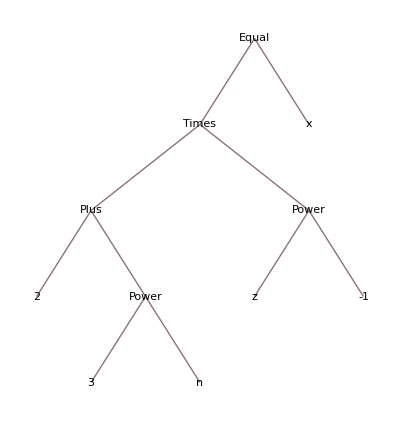

```mathematica
TreeForm[(a+b^n)/z==x]
```

表达式的完整形式

```mathematica
FullForm[(a+b^n)/z==x]
```

Equal[Times[Plus[2,Power[3,n]],Power[z,-1]],x]

常见运算符的完整形式

```mathematica
FullForm/@{a+b,a-b,a*b,a/b,a^b,a==b,a!=b,a<b,a<=b,a>b,a>=b,a&&b,a||b}
```

{5,-1,6,Rational[2,3],8,False,True,True,True,False,False,And[2,3],Or[2,3]}

语言也是一个表达式

```mathematica
ForAll[ϵ,ϵ>0,Exists[δ,δ>0,ForAll[x,Abs[x-Subscript[x, 0]]<δ,Abs[f[x]-f[Subscript[x, 0]]]<ϵ]]]//TraditionalForm
```

∀_(ϵ,ϵ>0)∃_(δ,δ>0)∀_(x,Abs[x-x_0]<δ)Abs[x^2-x_0^2]<ϵ

## 表达式的计算法则

```mathematica
Trace[(#2-#1)&@@(Integrate[Sin[x]^2,x]/.{x->#}&/@{0,2Pi})]//StandardForm
```

{{(∫Sin[x]^2 ⅆx/.{x→#1}&)/@{0,2 π},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π]},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[0],∫Sin[x]^2 ⅆx/.{x→0},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→0,x→0},{x→0}},x/2-1/4 Sin[2 x]/.{x→0},0/2-1/4 Sin[2 0],{0/2,0},{{{2 0,0},Sin[0],0},-0/4,0},0+0,0},{(∫Sin[x]^2 ⅆx/.{x→#1}&)[2 π],∫Sin[x]^2 ⅆx/.{x→2 π},{∫Sin[x]^2 ⅆx,x/2-1/4 Sin[2 x]},{{x→2 π,x→2 π},{x→2 π}},x/2-1/4 Sin[2 x]/.{x→2 π},(2 π)/2-1/4 Sin[2 (2 π)],{(2 π)/2,(2 π)/2,π},{{{2 (2 π),2 2 π,4 π},Sin[4 π],0},-0/4,0},π+0,π},{0,π}},(#2-#1&)@@{0,π},(#2-#1&)[0,π],π-0,{-0,0},π+0,π}

## 表达式与表